# Point Particle Coulomb Repulsion

## Matt Kafker July 26, 2022

## Equation of Motion, Analytical Solution t(x)

From energy conservation, we derive the differential equation governing the inter-particle separation

	ẋ = √(2/μ(ℰ-(k q_1 q_2)/(|x|)))
	
which can be solved by integration

		∫_x_0^x (d x̃)/(x̃) = ∫_0^t d t̃

```mathematica
FullSimplify[Assuming[ℰ>0&&k>0&&q1>0&&q2>0&&μ>0&&y∈Reals&&y>30&&(k q1 q2)/30<ℰ,∫_30^y 1/(√(2/µ(ℰ-(k q1 q2)/x)))ⅆx]/.y->x]
```

(k q1 q2 (-√((x ℰ (-k q1 q2+30 ℰ))/µ)+√30 √((ℰ (-k q1 q2+x ℰ))/µ))+x ℰ √((x ℰ (-k q1 q2+30 ℰ))/µ)-30 √30 ℰ^(3/2) √((-k q1 q2+x ℰ)/µ)+k q1 q2 (-√(((k q1 q2-30 ℰ) (k q1 q2-x ℰ))/µ) ArcTanh[√(1-(k q1 q2)/(30 ℰ))]+√((k q1 q2-30 ℰ) (k q1 q2-x ℰ)) √(1/µ) ArcTanh[√(1-(k q1 q2)/(x ℰ))]))/(ℰ^(3/2) √((-2 k q1 q2+60 ℰ)/µ) √((-k q1 q2+x ℰ)/µ))

```mathematica
t[x_]:=(k q1 q2 (-√((x ℰ (-k q1 q2+30 ℰ))/µ)+√30 √((ℰ (-k q1 q2+x ℰ))/µ))+x ℰ √((x ℰ (-k q1 q2+30 ℰ))/µ)-30 √30 ℰ^(3/2) √((-k q1 q2+x ℰ)/µ)+k q1 q2 (-√(1/µ(k q1 q2-30 ℰ) (k q1 q2-x ℰ)) ArcTanh[√(1-(k q1 q2)/(30 ℰ))]+√((k q1 q2-30 ℰ) (k q1 q2-x ℰ)) √(1/µ) ArcTanh[√(1-(k q1 q2)/(x ℰ))]))/(ℰ^(3/2) √((-2 k q1 q2+60 ℰ)/µ) √((-k q1 q2+x ℰ)/µ))
```

Substituting numerical values for the problem at hand

```mathematica
tnum[x_]:=FullSimplify[t[x]/.{ℰ->273.78603191489367
,k->1.44,q1->36,q2->56,µ->51860.16309012876}]
```

```mathematica
tnum[x]
```

-349.306+0.588153 √x √(-2903.04+273.786 x)+103.19 ArcTanh[√((-10.6033+x)/x)]

```mathematica
tnum[x]//TeXForm
```

0.588153 \sqrt{x} \sqrt{273.786 x-2903.04}+103.19 \tanh
   ^{-1}\left(\sqrt{\frac{x-10.6033}{x}}\right)-349.306

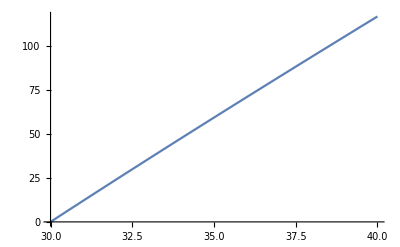

```mathematica
Plot[tnum[x],{x,30,40}]
```

## Numerically Inverting to Find x(t)

```mathematica
ts=0.06*Range[0,1666,1];
```

```mathematica
xrelanalytical=ParallelMap[FindRoot[tnum[x]==#,{x,30}]&,ts]//Transpose//Values//Part[#,1]&;
```

Testing the “analytical” solution x(t).

```mathematica
Max[Abs[Map[tnum,xrelanalytical]-ts]]
```

3.05533×10^-13